```mathematica
ClearAll[makeAPI,args,func,frmt]
makeAPI[args_List,func_Function,frmt_String]:=APIFunction[
args,
func,
frmt
];
ClearAll[makeCD,args,func,frmt]
makeCD[args_List,func_Function,frmt_String,endPoint_String,funcName_String,permit_String]:=CloudDeploy[
makeAPI[args,func,frmt],
"/" <> endPoint <> "/" <> funcName <> "/",
Permissions->"Public"
];
```

```mathematica
ClearAll[args,func,frmt,params]
args={"x"->Interpreter["Integer"], "y"->Interpreter["Integer"]};
func = Function[RandomInteger[{#x,#y}]];
frmt="JSON";

params = <|"x"->-10,"y"->10|>;
makeAPI[args,func,frmt][params]
```

-5

```mathematica
endPoint = "coursework/unitTest";
funcName = "random-integer";
permit = "Public";
makeCD[args,func,frmt,endPoint,funcName,permit]
```

CloudObject[https://www.wolframcloud.com/obj/85100044/coursework/unitTest/random-integer]

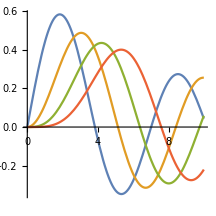

{{360,360},1,1.}

```mathematica
ClearAll[plt,di,ndi,xPX,yPX,xAR,yAR]
di=72;
ndi=3;

xAR = 1;
yAR=1;
xPX = di*ndi;
yPX = xPX*(yAR/xAR);

plt=Plot[
Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},
ImageSize->{xPX,yPX},
AspectRatio->yAR/xAR
];

Framed[plt,
FrameMargins->{{0,0},{0,0}},
ContentPadding->False,
FrameStyle->Gray
]

{ImageDimensions[plt],ImageAspectRatio[plt],N@ImageAspectRatio[plt]}
```

```mathematica
ClearAll[wPX,hPX]
(*bp = base )or known) pixels of either x (w) or y(h)*)
wPX[base_]:=base
wPX[base_,w_,h_]:=base*(w/h)
hPX[base_]:=base
hPX[base_,w_,h_]:=base*(h/w)
```

```mathematica
bpW = 72*2;
wPX[bpW]
hPX[bpW,16,9]
%/%%
```

144

81

9/16

```mathematica
bpH = 72*2;
wPX[bpH,16,9]
hPX[bpH]
%/%%
```

256

144

9/16

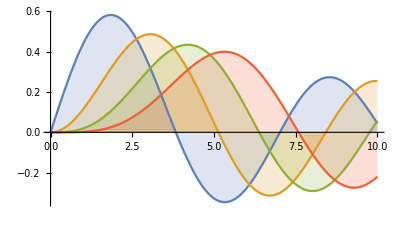

{{667,375},375/667,0.562219}

```mathematica
ClearAll[plt,bp,bpW,bpH,w,h]
bpW=400;
w=16;
h=9;
ClearAll[plt]
plt=Plot[
Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis,
ImageSize->{wPX[bpW],hPX[bpW,w,h]},
AspectRatio->hPX[bpW,w,h]/wPX[bpW]
];

Framed[plt]

{ImageDimensions[plt],ImageAspectRatio[plt],N@ImageAspectRatio[plt]}
```

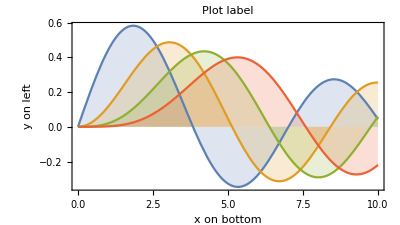

{{667,375},375/667,0.562219}

```mathematica
ClearAll[plt,bp,bpW,bpH,w,h]
bpW=400;
w=16;
h=9;
ClearAll[plt]
plt=Plot[
Evaluate[Table[BesselJ[n,x],{n,4}]],{x,0,10},Filling->Axis,
ImageSize->{wPX[bpW],hPX[bpW,w,h]},
AspectRatio->hPX[bpW,w,h]/wPX[bpW],
PlotLabel->Style["Plot label",9],
(*PlotLegends->Placed[{"1","2","3","4"},Below],*)
Frame->True,
FrameTicks->{{Automatic,None},{Automatic,None}},
FrameTicksStyle->Directive[Black,8],
FrameLabel->{Style[#,8]&/@{"y on left","y on right"},Style[#,8]&/@{"x on bottom","x on top"}}
];

Framed[plt,
FrameMargins->{{0,0},{0,0}},
ContentPadding->False,
FrameStyle->Gray
]

{ImageDimensions[plt],ImageAspectRatio[plt],N@ImageAspectRatio[plt]}
```

```mathematica
ClearAll[equ]
equ=1+a*x^2+Sqrt[(b*y^3)/(a+x)]
equ//Head
equ//FullForm
```

1+a x^2+√((b y^3)/(a+x))

Plus

Plus[1,Times[a,Power[x,2]],Power[Times[b,Power[Plus[a,x],-1],Power[y,3]],Rational[1,2]]]

```mathematica
Framed[equ,
FrameMargins->{{0,0},{0,0}},
ContentPadding->False,
FrameStyle->Gray
]
```

1+a x^2+√((b y^3)/(a+x))

```mathematica
ClearAll[rstr]
rstr = Rasterize[
Framed[equ,
FrameMargins->{{0,0},{0,0}},
ContentPadding->False,
FrameStyle->Gray,
ImageSize->{200,100},
Alignment->{Center,Center}
]
]
rsrt//Head
{ImageDimensions[rstr],ImageAspectRatio[rstr],N@ImageAspectRatio[rstr]}
```

-Graphics-

Symbol

{{334,170},85/167,0.508982}

```mathematica
ClearAll[rstr,bpW,w,h,fs,rsMult]
bpW=72*2;
w=16;
h=9;
fs=12;
rsMult=13;

rstr = Rasterize[
Framed[
Item[Style[equ,FontFamily->"Arabic Transparent", FontSize->fs],Alignment->{Center,Center}],
(*equ*)
FrameMargins->{{0,0},{0,0}},
ContentPadding->False,
FrameStyle->Directive[Gray,Thickness[1]],
ImageSize->{wPX[bpW],hPX[bpW,w,h]}
(*RoundRadius->10,*)
],
RasterSize->rsMult*bpW,
Background->LightYellow
]
rsrt//Head
{ImageDimensions[rstr],ImageAspectRatio[rstr],N@ImageAspectRatio[rstr]}
```

-Graphics-

Symbol

{{1872,1079},83/144,0.576389}

```mathematica
ClearAll[eq]
eq=Solve[x^2+a*x+1==0,x];
eq
eq//Head
eq//FullForm
```

{{x→1/2 (-a-√(-4+a^2))},{x→1/2 (-a+√(-4+a^2))}}

List

List[List[Rule[x,Times[Rational[1,2],Plus[Times[-1,a],Times[-1,Power[Plus[-4,Power[a,2]],Rational[1,2]]]]]]],List[Rule[x,Times[Rational[1,2],Plus[Times[-1,a],Power[Plus[-4,Power[a,2]],Rational[1,2]]]]]]]

```mathematica
eq[[1,1,1]]
```

x